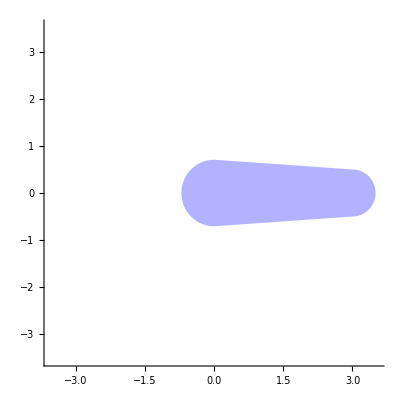

```mathematica
NumericalRangeVisual[
DirectSum[{{3, 1}, {0, 3}}, {{0, 1, 0}, {0, 0, 1}, {0, 0, 0}}]
]
```

```mathematica
DirectSum[{{3, 1}, {3, 0}}, {{0, 1, 0}, {0, 0, 1}, {0, 0, 0}}] // MatrixForm
```

(3 | 1 | 0 | 0 | 0
3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0)

```mathematica
A = DirectSum[
DirectSum[{{-2, 1}, {0, -2}}, {{2, 1}, {0, 2}}],
DirectSum[{{3 I, 1, 0}, {0, 3 I, 1}, {0, 0, 3 I}},{{-I, 1, 0, 0}, {0, -I, 1, 0}, {0, 0, -I, 1}, {0, 0, 0, -I}}]
];
```

```mathematica
Krug[{x_, y_}, n_] := Graphics[{Red, Disk[{x, y}, Cos[π/n]]}];
```

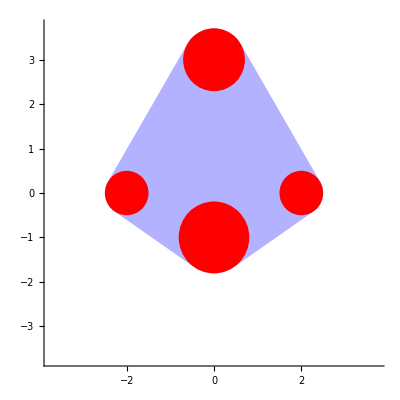

```mathematica
Show[{NumericalRangeVisual[A], Krug[{-2, 0}, 3], Krug[{2, 0}, 3], Krug[{0, 3}, 4], Krug[{0, -1}, 5]}]
```

```mathematica
Export["Jordan.eps", %]
```

Jordan.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Jordan.eps"]]]
```

```mathematica
S = DirectSum[
DirectSum[{{1, 0}, {2, 1}}, {{1, -2}, {0, 1}}],
DirectSum[{{1, 0, 0}, {2,1, 0}, {3, 3, 1}}, {{1, 0, 0, 0}, {-1, 1, 0, 0}, {-2, -3, 1, 0}, {1, 0, 1, 1}}]
];
```

```mathematica
S // MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
S = DirectSum[{{1, 0}, {2, 1}}, IdentityMatrix[9]];
```

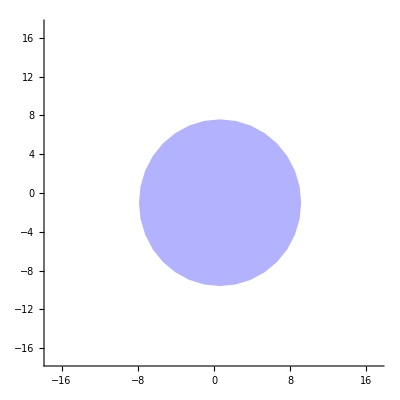

```mathematica
NumericalRangeVisual[Inverse[S] . A . S]
```

```mathematica
Export["slicna.eps", %]
```

slicna.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["slicna.eps"]]]
```